```mathematica
Clear["Global`*"]
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
SetOptions[{Plot,ListPlot,LogPlot,LogLogPlot,ListLinePlot,ListLogLogPlot},Frame->True,Axes->False,GridLines->None,ImageSize->500,(*Apply the high-contrast colors and thickness*)PlotStyle->(Directive[AbsoluteThickness[1.5]]),(*Force deep black frame and tick numbers*)FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontSize->18],(*Base style for any text that isn't MaTeX*)BaseStyle->{FontFamily->"Latin Modern Roman 12",FontSize->18}];
```

```mathematica
SetOptions[{ParametricPlot,ParametricPlot3D},Axes->False,ImageSize->500,(*Apply the high-contrast colors and thickness*)PlotStyle->(Directive[AbsoluteThickness[1.5]]),(*Force deep black frame and tick numbers*)(*Base style for any text that isn't MaTeX*)BaseStyle->{FontFamily->"Latin Modern Roman 12",FontSize->18}];
```

```mathematica
SetOptions[MaTeX,"FontSize"->18];
```

```mathematica
ar=2 0.5;(*aspect ratio*)
ntheta=40;
nphi=40(*40*)(*ar ntheta/2*);
nPart=10;
nSq=20;
```

```mathematica
40 40
```

1600

```mathematica
symboliclegendre[n_,x_]:=Solve[LegendreP[n,x]==0];
legendreprime[n_,a_]:=D[LegendreP[n,x],x]/. x->a;
weights[n_,x_]:=2/((1-x^2) legendreprime[n,x]^2);
```

```mathematica
xlist=x/.symboliclegendre[ntheta,x];
roots=N[xlist,15];
xPart=x/.symboliclegendre[nPart,x];
rootsPart=N[xPart,15];
xSq=x/.symboliclegendre[nSq,x];
rootsSq=N[xSq,15];
```

```mathematica
aL=3.3333;
(*select rod radius here:*)
a=1/6;
Lval=x/.NSolve[√(1-a^2)+x==aL/2,x,Reals][[1]]
```

0.680637

#### Neck parameterization:

```mathematica
R=1;
L=Lval;
a=R/6;
zc=√(R^2-a^2);
thc=ArcSin[a/R];

t[s_]:=(s+1)/2;

H[t_]:=Exp[-1/t]/(Exp[-1/t]+Exp[-1/(1-t)])(*Piecewise[{{0,t<=0},{Exp[-1/t]/(Exp[-1/t]+Exp[-1/(1-t)]),0<t<1},{1,t>=1}}];*)

thetaS[s_]:=thc (1-t[s]);

rhoS[s_]:=R Sin[thetaS[s]];
zS[s_]:=R Cos[thetaS[s]];

rhoC[s_]:=a;
zC[s_]:=zc+L t[s];

rho[s_]:=(1-H[t[s]]) rhoS[s]+H[t[s]] rhoC[s];

z[s_]:=(1-H[t[s]]) zS[s]+H[t[s]] zC[s];

X[s_,phi_]:={rho[s] Cos[phi],rho[s] Sin[phi],z[s]};
```

General::munfl: Exp[-48951.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

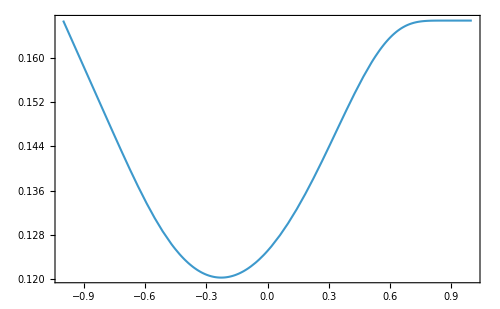

```mathematica
Plot[rho[s],{s,-1,1}]
```

```mathematica
1/2 NIntegrate[rho[s],{s,-1,1}]
```

0.143698

```mathematica
RotateX[x_,w_]:=
{{1,0,0},
{0,Cos[w],Sin[w]},
{0,-Sin[w],Cos[w]}}.x;
```

```mathematica
RotateY[x_,w_]:=
{{Cos[w],0,Sin[w]},
{0,1,0},
{-Sin[w],0,Cos[w]}}.x;
```

```mathematica
2(zc+L)//N
```

3.3333

#### full-square grid:

```mathematica
u1=rootsSq;
u2=rootsSq;
```

```mathematica
wgts1=N[weights[nSq,xSq],15];
wgts2=N[weights[nSq,xSq],15];
fSqPt=Tuples[{u1,u2}];
wgFSq=Tuples[{wgts1,wgts2}];
```

```mathematica
fSqPt//Dimensions
```

{400,2}

#### rod grid:

```mathematica
sPt=(roots);
phiPt=Table[(2π)/nphi(j-1),{j,1,nphi}]//N;
wgtsS=N[weights[ntheta,xlist],15];
wgtsPhi=2 π/nphi Table[1,nphi];
rodPt=Tuples[{sPt,phiPt}];
wgtsRod=Tuples[{wgtsS,wgtsPhi}];
```

#### partial-square grid:

```mathematica
wgtsPart=N[weights[nPart,xPart],15];
```

```mathematica
sec1=Flatten[Table[{Tan[thc]+(Sec[p]-Tan[thc])(r+1)/2,p},{p,π/4 rootsPart},{r,rootsPart}],1];
sec2=Flatten[Table[{Tan[thc]+(Csc[p]-Tan[thc])(r+1)/2,p},{p,π/2+π/4 rootsPart},{r,rootsPart}],1];
sec3=Flatten[Table[{Tan[thc]+(-Sec[p]-Tan[thc])(r+1)/2,p},{p,π+π/4 rootsPart},{r,rootsPart}],1];
sec4=Flatten[Table[{Tan[thc]+(-Csc[p]-Tan[thc])(r+1)/2,p},{p,(3π)/2+π/4 rootsPart},{r,rootsPart}],1];
```

```mathematica
wgSec1=Flatten[Table[{(Sec[π/4 rootsPart[[k]]]-Tan[thc])/2 wgtsPart[[r]],π/4 wgtsPart[[k]]},{k,1,Length@wgtsPart},{r,1,Length@wgtsPart}],1];
```

```mathematica
Total[wgSec1[[All,1]]wgSec1[[All,2]]]
```

1.4972341342466

```mathematica
pSqPt=Join[sec1,sec2,sec3,sec4];
pSqPt//Dimensions
```

{400,2}

```mathematica
wgtsPSqPt=Join[wgSec1,wgSec1,wgSec1,wgSec1];
```

```mathematica
neckFn[r_,p_]:={r Cos[p],r Sin[p],1}/(√(1+r^2));
```

```mathematica
(*Graphics3D[{Point[Table[neckFn[pSqPt[[k,1]],pSqPt[[k,2]]],{k,1,Length@pSqPt}]],Red,
Point[Table[X[rodPt[[k,1]],rodPt[[k,2]]],{k,1,Length@rodPt}]]}]*)
```

```mathematica
(*ParametricPlot3D[{X[Cos[th],phi],{R Sin[th]  Cos[phi],R Sin[th] Sin[phi],R Cos[th]},
-X[Cos[th],phi]+2{0,0,zc+L},{R Sin[th]  Cos[phi],R Sin[th] Sin[phi],R Cos[th]+2(zc+L)},
RotateX[X[Cos[th],phi],π/2],-RotateX[X[Cos[th],phi],π/2]+2{0,zc+L,0},{R Sin[th]  Cos[phi],R Sin[th] Sin[phi]+2(zc+L),R Cos[th]},
X[Cos[th],phi]+2{0,zc+L,0},-X[Cos[th],phi]+2{0,zc+L,zc+L},{R Sin[th]  Cos[phi],R Sin[th] Sin[phi]+2(zc+L),R Cos[th]+2(zc+L)},
RotateX[X[Cos[th],phi],π/2]+2{0,0,zc+L},-RotateX[X[Cos[th],phi],π/2]+2{0,zc+L,zc+L}
},{th,thc,π},{phi,0,2π},PlotStyle->{Automatic,Opacity[0.4]},PlotRange->All]*)
```

```mathematica
Show[ParametricPlot3D[{X[s,phi](*,
RotateX[X[s,phi],π/2],
RotateY[X[s,phi],π/2]*)
},{s,-1,1},{phi,0,2π},PlotStyle->{Automatic,Opacity[0.4]},PlotRange->All,Axes->False,Mesh->5],
ParametricPlot3D[{r Cos[p],r Sin[p],1}/(√(1+r^2)),{p,-π/4,π/4},{r,Tan[thc],1/Cos[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{r Cos[p],r Sin[p],1}/(√(1+r^2)),{p,π/4,3π/4},{r,Tan[thc],1/Sin[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{r Cos[p],r Sin[p],1}/(√(1+r^2)),{p,3π/4,5π/4},{r,Tan[thc],-1/Cos[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{r Cos[p],r Sin[p],1}/(√(1+r^2)),{p,5π/4,7π/4},{r,Tan[thc],-1/Sin[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{u,-1,v}/(√(1+u^2+v^2)),{u,-1,1},{v,-1,1},PlotRange->All,Mesh->5],
ParametricPlot3D[{u,v,-1}/(√(1+u^2+v^2)),{u,-1,1},{v,-1,1},PlotRange->All,Mesh->5],
ParametricPlot3D[{-1,u,v}/(√(1+u^2+v^2)),{u,-1,1},{v,-1,1},PlotRange->All,Mesh->5],
(*another partial patch*)
ParametricPlot3D[{r Cos[p],1,r Sin[p]}/(√(1+r^2)),{p,-π/4,π/4},{r,Tan[thc],1/Cos[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{r Cos[p],1,r Sin[p]}/(√(1+r^2)),{p,π/4,3π/4},{r,Tan[thc],1/Sin[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{r Cos[p],1,r Sin[p]}/(√(1+r^2)),{p,3π/4,5π/4},{r,Tan[thc],-1/Cos[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{r Cos[p],1,r Sin[p]}/(√(1+r^2)),{p,5π/4,7π/4},{r,Tan[thc],-1/Sin[p]},PlotRange->All,Mesh->5],
(*another partial patch*)
ParametricPlot3D[{1,r Cos[p],r Sin[p]}/(√(1+r^2)),{p,-π/4,π/4},{r,Tan[thc],1/Cos[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{1,r Cos[p],r Sin[p]}/(√(1+r^2)),{p,π/4,3π/4},{r,Tan[thc],1/Sin[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{1,r Cos[p],r Sin[p]}/(√(1+r^2)),{p,3π/4,5π/4},{r,Tan[thc],-1/Cos[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{1,r Cos[p],r Sin[p]}/(√(1+r^2)),{p,5π/4,7π/4},{r,Tan[thc],-1/Sin[p]},PlotRange->All,Mesh->5],
ParametricPlot3D[{RotateX[X[s,phi],π/2](*,
RotateX[X[s,phi],π/2],
RotateY[X[s,phi],π/2]*)
},{s,-1,1},{phi,0,2π},Mesh->5],
ParametricPlot3D[{RotateY[X[s,phi],π/2](*,
RotateX[X[s,phi],π/2],
RotateY[X[s,phi],π/2]*)
},{s,-1,1},{phi,0,2π},Mesh->5]
]
```

General::munfl: Exp[-13986.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
rod=Map[X[#[[1]],#[[2]]]&,rodPt];
```

General::munfl: 0.986613 3.62743409×10^-493 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
nRodFn=-Cross[D[X[s,phi],s],D[X[s,phi],phi]];
```

```mathematica
nRodVal=Map[nRodFn/.{s->#[[1]],phi->#[[2]]}&,rodPt];
```

General::munfl: 4.35963×10^-29 1.177435286×10^-281 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.23268×10^-30 (-1.412922343×10^-280) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.19991×10^-30 4.23876703×10^-280 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
nRodVal[[3]]
```

{0.0561421,0.0182417,-0.00429747}

```mathematica
xZ={u,v,-1}/(√(1+u^2+v^2));
nZ=-Cross[D[xZ,u],D[xZ,v]]//Simplify
```

{u/((1+u^2+v^2)^2),v/((1+u^2+v^2)^2),-1/((1+u^2+v^2)^2)}

```mathematica
xY={u,-1,v}/(√(1+u^2+v^2));
nY=Cross[D[xY,u],D[xY,v]]//Simplify
```

{u/((1+u^2+v^2)^2),-1/((1+u^2+v^2)^2),v/((1+u^2+v^2)^2)}

```mathematica
xX={-1,u,v}/(√(1+u^2+v^2));
nX=-Cross[D[xX,u],D[xX,v]]//Simplify
```

{-1/((1+u^2+v^2)^2),u/((1+u^2+v^2)^2),v/((1+u^2+v^2)^2)}

```mathematica
fSqPt//Dimensions
```

{400,2}

```mathematica
sFullPatchX=Map[xX/.{u->#[[1]],v->#[[2]]}&,fSqPt];
sFullPatchY=Map[xY/.{u->#[[1]],v->#[[2]]}&,fSqPt];
sFullPatchZ=Map[xZ/.{u->#[[1]],v->#[[2]]}&,fSqPt];
```

```mathematica
nZVal=Map[nZ/.{u->#[[1]],v->#[[2]]}&,fSqPt];
nXVal=Map[nX/.{u->#[[1]],v->#[[2]]}&,fSqPt];
nYVal=Map[nY/.{u->#[[1]],v->#[[2]]}&,fSqPt];
```

```mathematica
xPZ={r Cos[p],r Sin[p],1}/(√(1+r^2));
nPZ=Cross[D[xPZ,r],D[xPZ,p]]//Simplify
```

{(r^2 Cos[p])/((1+r^2)^2),(r^2 Sin[p])/((1+r^2)^2),r/((1+r^2)^2)}

```mathematica
xPY={r Sin[p],1,r Cos[p]}/(√(1+r^2));
nPY=Cross[D[xPY,r],D[xPY,p]]//Simplify
```

{(r^2 Sin[p])/((1+r^2)^2),r/((1+r^2)^2),(r^2 Cos[p])/((1+r^2)^2)}

```mathematica
xPX={1,r Cos[p],r Sin[p]}/(√(1+r^2));
nPX=Cross[D[xPX,r],D[xPX,p]]//Simplify
```

{r/((1+r^2)^2),(r^2 Cos[p])/((1+r^2)^2),(r^2 Sin[p])/((1+r^2)^2)}

```mathematica
sPrtPatchX=Map[xPX/.{r->#[[1]],p->#[[2]]}&,pSqPt];
sPrtPatchY=Map[xPY/.{r->#[[1]],p->#[[2]]}&,pSqPt];
sPrtPatchZ=Map[xPZ/.{r->#[[1]],p->#[[2]]}&,pSqPt];
```

```mathematica
nPZVal=Map[nPZ/.{r->#[[1]],p->#[[2]]}&,pSqPt];
nPXVal=Map[nPX/.{r->#[[1]],p->#[[2]]}&,pSqPt];
nPYVal=Map[nPY/.{r->#[[1]],p->#[[2]]}&,pSqPt];
```

```mathematica
sPrtPatchX//Dimensions
```

{400,3}

```mathematica
nRodVal//Dimensions
```

{1600,3}

```mathematica
nRodVal//Mean
```

{-2.02963×10^-18,-4.39102×10^-19,0.00203492}

```mathematica
(*Graphics3D[{Point[rod],Blue,Table[Arrow[{rod[[k]],rod[[k]]+0.5Normalize@ nRodVal[[k]]}],{k,1,Length@rod,5}]}]*)
```

```mathematica
sFullPatchX//Dimensions
```

{400,3}

```mathematica
(*Graphics3D[{Point[sFullPatchX],Point[sFullPatchY],Point[sFullPatchZ],
Point[sPrtPatchX],Point[sPrtPatchY],Point[sPrtPatchZ],Blue,Table[Arrow[{sPrtPatchX[[k]],sPrtPatchX[[k]]+0.5 Normalize@nPXVal[[k]]}],{k,1,Length@nPXVal,8}](*,
Table[Arrow[{sFullPatchY[[k]],sFullPatchY[[k]]+0.5 Normalize@nYVal[[k]]}],{k,1,Length@nYVal,8}],
Table[Arrow[{sFullPatchZ[[k]],sFullPatchZ[[k]]+0.5 Normalize@nZVal[[k]]}],{k,1,Length@nZVal,8}]*),
Table[Arrow[{sPrtPatchY[[k]],sPrtPatchY[[k]]+0.5 Normalize@nPYVal[[k]]}],{k,1,Length@nPYVal,8}],
Table[Arrow[{sPrtPatchZ[[k]],sPrtPatchZ[[k]]+0.5 Normalize@nPZVal[[k]]}],{k,1,Length@nPZVal,8}]
}]*)
```

```mathematica
wgtsRodSurf=wgtsRod[[All,1]]wgtsRod[[All,2]]Map[Norm,nRodVal];
```

```mathematica
wgFSq//Dimensions
```

{400,2}

```mathematica
wgtsfulSZSurf=wgFSq[[All,1]]wgFSq[[All,2]]Map[Norm,nZVal];(*same for X and Z patches*)
```

```mathematica
wgtsPrtSZSurf=wgtsPSqPt[[All,1]]wgtsPSqPt[[All,2]]Map[Norm,nPZVal];(*same for X and Z patches*)
```

```mathematica
Total[wgtsfulSZSurf]
```

2.0943951023932

```mathematica
Total[wgtsPrtSZSurf]
```

2.0065140567593

```mathematica
wgtsPrtSZSurf//Dimensions
sPrtPatchZ//Dimensions
```

{400}

{400,3}

```mathematica
translateFn[x_,a_]:=x+a
invFn[x_,d_]:=DiagonalMatrix[d].x
```

```mathematica
1.659/9 8.750
```

1.61292

#### For each collocation point, we now have normal and weight! To generate rest of structure, just use rotation and translation transformations.

```mathematica
cell1=Join[sFullPatchX,sFullPatchY,sFullPatchZ,sPrtPatchX,sPrtPatchY,sPrtPatchZ,rod,Map[RotateX[#,π/2]&,rod],Map[RotateY[#,π/2]&,rod]];
nCell1=Join[nXVal,nYVal,nZVal,nPXVal,nPYVal,nPZVal,nRodVal,Map[RotateX[#,π/2]&,nRodVal],Map[RotateY[#,π/2]&,nRodVal]];
wgtCell1=Join[wgtsfulSZSurf,wgtsfulSZSurf,wgtsfulSZSurf,wgtsPrtSZSurf,wgtsPrtSZSurf,wgtsPrtSZSurf,wgtsRodSurf,wgtsRodSurf,wgtsRodSurf];
```

```mathematica
cell2=translateFn[RotateX[#,π/2],2(zc+L){0,0,1}]&/@cell1;
nCell2=RotateX[#,π/2]&/@nCell1;
wgtCell2=wgtCell1;
```

```mathematica
cell3=translateFn[RotateX[#,-π/2],2(zc+L){0,1,0}]&/@cell1;
nCell3=RotateX[#,-π/2]&/@nCell1;
wgtCell3=wgtCell1;
```

```mathematica
cell4=translateFn[RotateX[#,π],2(zc+L){0,1,1}]&/@cell1;
nCell4=RotateX[#,π]&/@nCell1;
wgtCell4=wgtCell1;
```

```mathematica
(*Graphics3D[{Point[cell1],Red,Point[cell2],Blue,Point[cell3],Green,Point[cell4]},Axes->True,AxesLabel->{"x","y","z"}]*)
```

```mathematica
upPart=Join[cell1,cell2,cell3,cell4];
nUpPart=Join[nCell1,nCell2,nCell3,nCell4];
wgtUpPart=Join[wgtCell1,wgtCell2,wgtCell3,wgtCell4];
```

```mathematica
upPart//Dimensions
nUpPart//Dimensions
wgtUpPart//Dimensions
```

{28800,3}

{28800,3}

{28800}

```mathematica
RotateZ[x_,w_]:={{Cos[w],-Sin[w],0},{Sin[w],Cos[w],0},{0,0,1}}.x
```

```mathematica
dwnPart=translateFn[RotateZ[#,π],2(zc+L){1,1,0}]&/@upPart;
nDwnPart=RotateZ[#,π]&/@nUpPart;
```

```mathematica
(*Graphics3D[{Point[upPart],Blue,Point[dwnPart]}]*)
```

```mathematica
sccFull=Join[upPart,dwnPart];
nScc=Join[nUpPart,nDwnPart];
wgtScc=Join[wgtUpPart,wgtUpPart];
```

```mathematica
xC=Total[sccFull wgtScc]/Total[wgtScc]
```

{1.66665,1.66665,1.66665}

```mathematica
sccFull//Norm
```

783.054

```mathematica
√3(2L+2zc)/2//N
```

2.88672

```mathematica
2(zc+L)//N
```

3.3333

```mathematica
Graphics3D[{Point[sccFull],Red,Point[xC](*,Blue,Table[Arrow[{sccFull[[k]],sccFull[[k]]+0.5Normalize@nScc[[k]]}],{k,1,Length@sccFull,20}]*)}]
```

-Graphics3D-

```mathematica
L
```

0.680637

```mathematica
8 4π R^2+12 2π a (2L)//N
```

117.637

```mathematica
a
```

1/6

#### Save to file:

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\cloudData\PhDWork\year2\bimBoundedSpectral\postProcess

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\sccStructRBy6\\sccCPL3p33.txt",sccFull,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\sccStructRBy6\sccCPL3p33.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\sccStructRBy6\\sccNVecL3p33.txt",Map[Normalize,nScc],"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\sccStructRBy6\sccNVecL3p33.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\sccStructRBy6\\sccWgtL3p33.txt",wgtScc,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\sccStructRBy6\sccWgtL3p33.txt

```mathematica
nNrml=Map[Normalize,nScc];
fvl=(1/3 Total[(Table[sccFull[[k]].nNrml[[k]],{k,1,Length@sccFull}]) wgtScc])/(4/3 π R^3)
```

8.25315

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\sccStructRBy6\\FvaL3p33.txt",fvl]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\sccStructRBy6\FvaL3p33.txt

```mathematica
2 L
```

1.36127

```mathematica
2(L+zc)//N
```

3.

```mathematica
3√3/2//N
```

2.59808

#### Weight of structure:

```mathematica
8+(9 a^2 2L)/R^3//N
```

9.34166

```mathematica
8+(12 π a^2 2L)/(4/3 π R^3)//N
```

9.34166

```mathematica
a
```

0.19305

```mathematica
(zc+L)2
```

5.96238

```mathematica
npdf fellow postdoc
```

### Test for mesh:

```mathematica
mshPt=ReadList["../outputData/sccCrystal/mesh/meshOut1.txt",{Number,Number,Number}];
mshPt//Dimensions
```

{57600,3}

```mathematica
Graphics3D[{Point[mshPt]},Axes->True]
```

-Graphics3D-

```mathematica
Total[mshPt]
```

{-7.01402×10^-9,-8.91305×10^-9,-6.80302×10^-9}

### For container:

```mathematica
128 5/2
```

320

```mathematica
nphi=64;
ntheta=192;
```

```mathematica
nphi ntheta
```

12288

```mathematica
Lbox = 2 125;(*length of the box*)
(*nY=128;*)
```

```mathematica
(*xlist=x/.symboliclegendre[nY,x];
roots=N[xlist,15];
nodes=Lbox/2(roots);
wgtsTheta=N[Lbox/2 weights[nY,xlist],15];*)
```

```mathematica
symboliclegendre[n_,x_]:=Solve[LegendreP[n,x]==0];
legendreprime[n_,a_]:=D[LegendreP[n,x],x]/. x->a;
weights[n_,x_]:=2/((1-x^2) legendreprime[n,x]^2);
```

```mathematica
xlist=x/.symboliclegendre[ntheta,x];
roots=N[xlist,15];
```

```mathematica
nodes=π/2(roots+1);
wgtsTheta=N[π/2 weights[ntheta,xlist],15];
```

Divide::infy: Infinite expression 1/(0``-117.56532005783338) encountered.

Power::infy: Infinite expression 1/(0``-59.16744400227555)^2 encountered.

Power::infy: Infinite expression 1/(0``-59.16744400227555)^2. encountered.

Power::infy: Infinite expression 1/(0``-59.70612697761545)^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Divide::infy: Infinite expression 1/(0``-117.5398561847641) encountered.

Divide::infy: Infinite expression 1/(0``-117.76231723605203) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

```mathematica
wgtsTheta//Dimensions
```

{192}

```mathematica
phiPt=Table[(2π)/nphi(j-1),{j,1,nphi}]//N;
thetaPt=Table[π/2(1+roots[[i]]),{i,1,ntheta}];
```

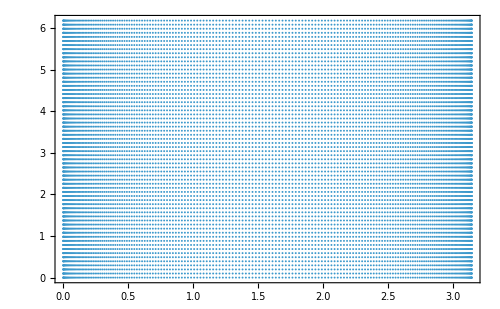

```mathematica
parametricPt=Tuples[{thetaPt,phiPt}//N];
ListPlot[parametricPt]
```

```mathematica
kappa=1;
rad=25;
```

```mathematica
(*borderFn[x_]:=rad √(1-((2x)/Lbox)^10);
Show[Plot[borderFn[x],{x,-Lbox/2,Lbox/2},PlotRange->All(*,Epilog->{PointSize[Medium],Red,Point[Transpose[{nodes,Map[borderFn,nodes]}]]}*)],
ContourPlot[x^10/(Lbox/2)^10+y^10/rad^10==1,{x,-Lbox/2,Lbox/2},{y,0,rad} ]
]*)
```

```mathematica
exp=10;
```

```mathematica
Show[ParametricPlot3D[{rad Sin[th]/((Cos[th]^exp+Sin[th]^exp)^(1/exp))Cos[phi]/((Cos[phi]^exp+Sin[phi]^exp)^(1/exp)),rad Sin[th]/((Cos[th]^exp+Sin[th]^exp)^(1/exp))Sin[phi]/((Cos[phi]^exp+Sin[phi]^exp)^(1/exp)),Lbox/2 Cos[th]/((Cos[th]^exp+Sin[th]^exp)^(1/exp))},{th,0,π},{phi,0,2π},ImageSize->Medium,Axes->True,Ticks->None,AxesLabel->{MaTeX["x"],MaTeX["y"],MaTeX["z"]},PlotStyle->Opacity[0.7]],
Graphics3D[{Opacity[1],Cuboid[{-1.4rad,-1.4 rad,0 Lbox/2},{1.4rad,1.4 rad,0.01}]}]]
```

-Graphics3D-

```mathematica
(*ParametricPlot3D[{borderFn[Lbox/2 Cos[th]] Cos[phi]/((Cos[phi]^exp+Sin[phi]^exp)^(1/exp)),borderFn[Lbox/2 Cos[th]] Sin[phi]/((Cos[phi]^exp+Sin[phi]^exp)^(1/exp)),Lbox/2 Cos[th]},{th,0,π},{phi,0,2π}]*)
```

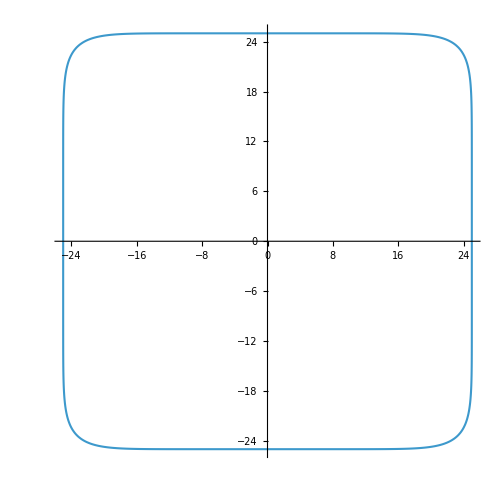

```mathematica
ParametricPlot[{rad{Cos[t]/((Cos[t]^exp+Sin[t]^exp)^(1/exp)),Sin[t]/((Cos[t]^exp+Sin[t]^exp)^(1/exp))}},{t,0,2π},PlotRange->All,(*Frame->True,*)Axes->True,AxesLabel->{MaTeX["x/a"],MaTeX["y/a"]}(*,GridLines->Automatic*)]
```

```mathematica
rad(2π)/nphi//N
```

2.45437

```mathematica
rad Abs[Differences[thetaPt]]//Min
```

0.640874128661513

```mathematica
uContainer[x_]:=0{0,1,0};
```

```mathematica
(*Parametric equation of container:*)
xC1=rad Sin[parametricPt[[All,1]]]/((Cos[parametricPt[[All,1]]]^exp+Sin[parametricPt[[All,1]]]^exp)^(1/exp)) Cos[parametricPt[[All,2]]]/((Cos[parametricPt[[All,2]]]^exp+Sin[parametricPt[[All,2]]]^exp)^(1/exp));
xC3=rad Sin[parametricPt[[All,1]]]/((Cos[parametricPt[[All,1]]]^exp+Sin[parametricPt[[All,1]]]^exp)^(1/exp)) Sin[parametricPt[[All,2]]]/((Cos[parametricPt[[All,2]]]^exp+Sin[parametricPt[[All,2]]]^exp)^(1/exp));
xC2=Lbox/2 Cos[parametricPt[[All,1]]]/((Cos[parametricPt[[All,1]]]^exp+Sin[parametricPt[[All,1]]]^exp)^(1/exp));
```

```mathematica
boxCollocationPt=Transpose[{xC1,xC2,xC3}];
```

```mathematica
Graphics3D[{Point[boxCollocationPt],Sphere[{-1.25,0,0},1],Sphere[{1.25,0 27,0},1]},PlotRange->All,Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
uContainerList=Map[uContainer,boxCollocationPt[[All,2]]];
```

```mathematica
uContainerList//Dimensions
```

{12288,3}

```mathematica
rad
```

25

```mathematica
Lbox
```

250

```mathematica
(*set normal vectors associated with each collocation point: eTheta x ePhi*)
rCVec={rad Sin[th]/((Cos[th]^exp+Sin[th]^exp)^(1/exp))Cos[phi]/((Cos[phi]^exp+Sin[phi]^exp)^(1/exp)),Lbox/2 Cos[th]/((Cos[th]^exp+Sin[th]^exp)^(1/exp)),rad Sin[th]/((Cos[th]^exp+Sin[th]^exp)^(1/exp)) Sin[phi]/((Cos[phi]^exp+Sin[phi]^exp)^(1/exp))};
eCTheta=D[rCVec,th];
eCPhi=D[rCVec,phi];
nCVec=Cross[eCTheta,eCPhi]//Simplify;(*not a unit vector...its magnitude carry jacobian factor*)
```

```mathematica
boxNormalVec=Table[nCVec/.{th->parametricPt[[m,1]],phi->parametricPt[[m,2]]},{m,1,Length@parametricPt}]//N;
```

```mathematica
Min@Map[Norm,boxNormalVec]
Max@Map[Norm,boxNormalVec]
```

0.0766071

6727.43

```mathematica
Graphics3D[{Point[boxCollocationPt],Table[Arrow[{boxCollocationPt[[k]],boxCollocationPt[[k]]+20Normalize@boxNormalVec[[k]]}],{k,1,Length@boxCollocationPt,10}]}]
```

-Graphics3D-

```mathematica
wgtCPt=Tuples[{wgtsTheta,2 π/nphi Table[1,nphi]}//N];(*uniform wgts for trapezoidal rule*)
```

```mathematica
wgtCPt[[1;;10]]
wgtCPt//Dimensions
```

{{0.0256344,0.0981748},{0.0256344,0.0981748},{0.0256344,0.0981748},{0.0256344,0.0981748},{0.0256344,0.0981748},{0.0256344,0.0981748},{0.0256344,0.0981748},{0.0256344,0.0981748},{0.0256344,0.0981748},{0.0256344,0.0981748}}

{12288,2}

```mathematica
boxWgtVec=wgtCPt[[All,1]]wgtCPt[[All,2]] Map[Norm,boxNormalVec];
```

```mathematica
boxWgtVec//Dimensions
```

{12288}

```mathematica
NumberForm[Total[boxWgtVec],15]
```

49860.7112149598

```mathematica
NIntegrate[Norm[nCVec],{th,0,π},{phi,0,2π}]
```

49869.1

```mathematica
8NIntegrate[Norm[nCVec],{th,0,π/2},{phi,0,π/2}]
```

49869.1

```mathematica
9/49869 100//N
```

0.0180473

```mathematica
NumberForm[Total[boxWgtVec],15]
```

49860.7112149598

```mathematica
(*surface integral of f(x)=f(collocationPts).wgtVec*)
NumberForm[Total[boxWgtVec],15]
```

49860.7112149598

```mathematica
(*reg=ParametricRegion[{borderFn[u]Cos[v],borderFn[u]Sin[v],u},{{u,-Lbox/2,Lbox/2},{v,0,2π}}];*)
(*Region[reg]*)
```

```mathematica
(*NumberForm[NIntegrate[1,{x,y,z}∈reg,AccuracyGoal->10,WorkingPrecision->15],15]*)
```

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\boxExp10\\boxCollocationPtsLessTst.txt",boxCollocationPt,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\boxExp10\boxCollocationPtsLessTst.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\boxExp10\\boxNormalVectorsLessTst.txt",Map[Normalize,boxNormalVec],"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\boxExp10\boxNormalVectorsLessTst.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\boxExp10\\boxWgtsLessTst.txt",boxWgtVec,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\boxExp10\boxWgtsLessTst.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\boxExp10\\boxVelLessTst.txt",uContainerList,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\boxExp10\boxVelLessTst.txt

```mathematica
nphi ntheta
```

12288

```mathematica
1/(6π)//N
```

0.0530516

#### Convergence for container discretization:

```mathematica
pts={};
```

```mathematica
AppendTo[pts,{ntheta,nphi,-0.92366476926887509}];
```

```mathematica
pts
```

{{212,32,-0.927329},{212,64,-0.923742},{212,128,-0.92346},{256,32,-0.92733},{256,64,-0.923855},{256,128,-0.923665}}

```mathematica
Partition[pts,4][[All,-2;;-1]]
```

{{{128,128,-0.922204},{128,256,-0.922122}},{{100,128,-0.919685},{100,256,-0.919543}},{{192,128,-0.923355},{192,256,-0.923315}}}

```mathematica
ptsNw=Partition[pts,4];
```

```mathematica
ptsNw[[1]]
```

{{128,32,-0.925177},{128,64,-0.922589},{128,128,-0.922204},{128,256,-0.922122}}

```mathematica
Table[k,{k,ptsNw}]
```

{{{128,32,-0.925177},{128,64,-0.922589},{128,128,-0.922204},{128,256,-0.922122}},{{100,32,-0.924681},{100,64,-0.920666},{100,128,-0.919685},{100,256,-0.919543}},{{192,32,-0.925331},{192,64,-0.923523},{192,128,-0.923355},{192,256,-0.923315}}}

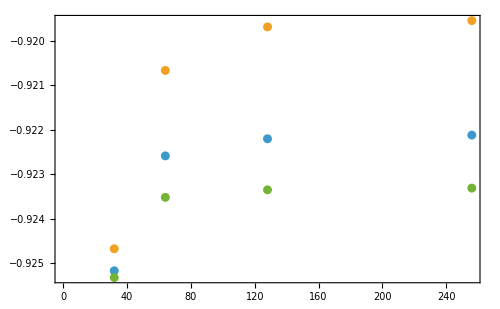

```mathematica
ListPlot[{pts[[1;;4,2;;-1]],pts[[5;;8,2;;-1]],pts[[9;;-1,2;;-1]]}]
```

```mathematica
Export["../outputData/convPtsSngleSphereExp10.txt",ptsSrt]
```

../outputData/convPtsSngleSphereExp10.txt

```mathematica
ptsSrt=ReadList["../outputData/convPtsSngleSphereExp10.txt"]
```

{{64,16,-0.939008},{64,32,-0.92231},{64,64,-0.949501},{64,128,-0.943708},{100,16,-0.939028},{100,28,-0.897712},{100,32,-0.926847},{100,64,-0.918967},{100,128,-0.912179},{100,256,-0.914063},{114,16,-0.93903},{114,32,-0.9271},{114,64,-0.921195},{114,128,-0.919244},{114,256,-0.919155},{128,16,-0.939029},{128,32,-0.927218},{128,64,-0.922257},{128,128,-0.921172},{128,256,-0.921281},{192,16,-0.939016},{192,32,-0.927327},{192,64,-0.923632},{192,128,-0.923285},{192,256,-0.92322}}

```mathematica
ptsSrt[[1;;4]]
```

{{64,16,-0.939008},{64,32,-0.92231},{64,64,-0.949501},{64,128,-0.943708}}

```mathematica
ptsSrt[[5;;10]]
```

{{100,16,-0.939028},{100,28,-0.897712},{100,32,-0.926847},{100,64,-0.918967},{100,128,-0.912179},{100,256,-0.914063}}

```mathematica
120 64
```

7680

```mathematica
ptsSrt[[16;;-1]]
```

{{128,16,-0.939029},{128,32,-0.927218},{128,64,-0.922257},{128,128,-0.921172},{128,256,-0.921281},{192,16,-0.939016},{192,32,-0.927327},{192,64,-0.923632},{192,128,-0.923285},{192,256,-0.92322}}

```mathematica
Abs@{ptsSrt[[{5,7,8,9,10}]],ptsSrt[[11;;15]],ptsSrt[[16;;20]],ptsSrt[[21;;-1]]}
```

{{{100,16,0.939028},{100,32,0.926847},{100,64,0.918967},{100,128,0.912179},{100,256,0.914063}},{{114,16,0.93903},{114,32,0.9271},{114,64,0.921195},{114,128,0.919244},{114,256,0.919155}},{{128,16,0.939029},{128,32,0.927218},{128,64,0.922257},{128,128,0.921172},{128,256,0.921281}},{{192,16,0.939016},{192,32,0.927327},{192,64,0.923632},{192,128,0.923285},{192,256,0.92322}}}

```mathematica
ptsSrt
```

{{64,16,-0.939008},{64,32,-0.92231},{64,64,-0.949501},{64,128,-0.943708},{100,16,-0.939028},{100,28,-0.897712},{100,32,-0.926847},{100,64,-0.918967},{100,128,-0.912179},{100,256,-0.914063},{114,16,-0.93903},{114,32,-0.9271},{114,64,-0.921195},{114,128,-0.919244},{114,256,-0.919155},{128,16,-0.939029},{128,32,-0.927218},{128,64,-0.922257},{128,128,-0.921172},{128,256,-0.921281},{192,16,-0.939016},{192,32,-0.927327},{192,64,-0.923632},{192,128,-0.923285},{192,256,-0.92322}}

```mathematica
ptsSrt
```

{{64,16,-0.939008},{64,32,-0.92231},{64,64,-0.949501},{64,128,-0.943708},{100,16,-0.939028},{100,28,-0.897712},{100,32,-0.926847},{100,64,-0.918967},{100,128,-0.912179},{100,256,-0.914063},{114,16,-0.93903},{114,32,-0.9271},{114,64,-0.921195},{114,128,-0.919244},{114,256,-0.919155},{128,16,-0.939029},{128,32,-0.927218},{128,64,-0.922257},{128,128,-0.921172},{128,256,-0.921281},{192,16,-0.939016},{192,32,-0.927327},{192,64,-0.923632},{192,128,-0.923285},{192,256,-0.92322}}

```mathematica
ptsSrt[[17]]
```

{128,32,-0.927218}

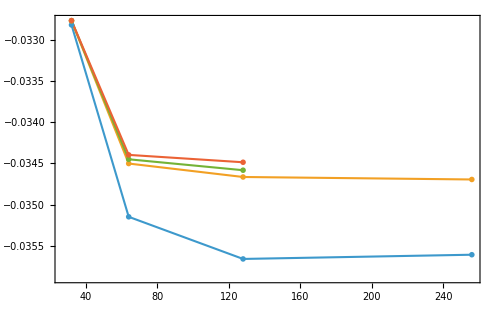

```mathematica
ListPlot[Abs@{(*ptsSrt[[{2+5,8,9,10},2;;3]],ptsSrt[[1+11;;15,2;;3]],*)ptsSrt[[1+16;;20,2;;3]],ptsSrt[[1+21;;-1,2;;3]],pts[[1;;3,2;;3]],pts[[4;;6,2;;3]]},PlotRange->All,ScalingFunctions->"Log10",Joined->True,PlotMarkers->"OpenMarkers",FrameLabel->{MaTeX["n_\\phi"], MaTeX["U_{1\\mathrm{sph}}/U_{1\\mathrm{sph}}^\\infty"]},PlotLegends->Placed[{MaTeX["n_\\theta = 128"],MaTeX["n_\\theta = 192"],MaTeX["n_\\theta = 212"],MaTeX["n_\\theta = 256"]},{Right,Top}]]
```

```mathematica
192 64
```

12288

```mathematica
1.730/0.92-1
```

0.880435

#### Checking capped cylinder data:

```mathematica
cppCylPts=ReadList["../meshData/boxExp10/boxCollocationPts.txt",{Number,Number,Number}];
```

```mathematica
cppCylNv=ReadList["../meshData/boxExp10/boxNormalVectors.txt",{Number,Number,Number}];
```

```mathematica
cppCylPts//Dimensions
```

{5120,3}

```mathematica
Graphics3D[{Point[cppCylPts],Red,Table[Arrow[{cppCylPts[[k]],cppCylPts[[k]]+20cppCylNv[[k]]}],{k,1,Length@cppCylNv,100}]}]
```

-Graphics3D-

### For rods:

```mathematica
aLBy2=6/2;
aR=0.9(aLBy2-1);
```

```mathematica
Lbox = 2 aR;(*length of the box*)
nY=40;
```

```mathematica
xlist=x/.symboliclegendre[nY,x];
roots=N[xlist,15];
nodes=Lbox/2(roots);
wgtsTheta=N[Lbox/2 weights[nY,xlist],15];
```

```mathematica
phiPt=Table[(2π)/nphi(j-1),{j,1,nphi}]//N;
thetaPt=Table[(Lbox/2 roots[[i]]),{i,1,nY}];
```

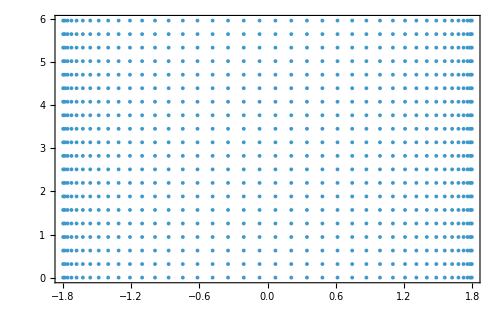

```mathematica
parametricPt=Tuples[{thetaPt,phiPt}//N];
ListPlot[parametricPt]
```

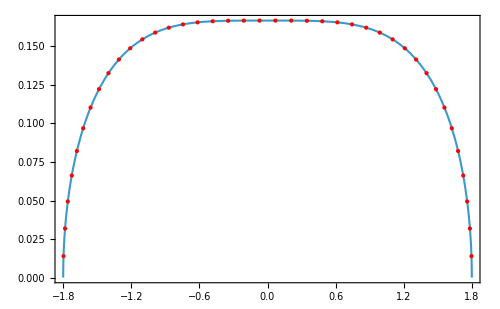

```mathematica
kappa=1;
rad=1/6;
borderFn[x_]:=rad √(1-((2x)/Lbox)^4);
Plot[borderFn[x],{x,-Lbox/2,Lbox/2},PlotRange->All,Epilog->{PointSize[Medium],Red,Point[Transpose[{nodes,Map[borderFn,nodes]}]]}]
```

```mathematica
uContainer[x_]:=0(1-borderFn[x]^2/(rad)^2){0,1,0};
```

```mathematica
(*Parametric equation of container:*)
xC1=borderFn[parametricPt[[All,1]]] Cos[parametricPt[[All,2]]];
xC3=borderFn[parametricPt[[All,1]]] Sin[parametricPt[[All,2]]];
xC2=parametricPt[[All,1]];
```

```mathematica
rodCollocationPt=Transpose[{xC1,xC2,xC3}];
```

```mathematica
Graphics3D[{Point[rodCollocationPt]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
(*set normal vectors associated with each collocation point: eTheta x ePhi*)
rCVec={borderFn[y] Cos[phi],y,borderFn[y] Sin[phi]};(*for spheroids*)
eCTheta=D[rCVec,y];
eCPhi=D[rCVec,phi];
nCVec=-Cross[eCTheta,eCPhi]//Simplify;(*not a unit vector...its magnitude carry jacobian factor*)
```

```mathematica
rodNormalVec=Table[nCVec/.{y->parametricPt[[m,1]],phi->parametricPt[[m,2]]},{m,1,Length@parametricPt}]//N;
```

```mathematica
Graphics3D[{Point[rodCollocationPt],Table[Arrow[{rodCollocationPt[[k]],rodCollocationPt[[k]]+2Normalize@rodNormalVec[[k]]}],{k,1,Length@rodCollocationPt,5}]}]
```

-Graphics3D-

```mathematica
wgtCPt=Tuples[{wgtsTheta,2 π/nphi Table[1,nphi]}//N];(*uniform wgts for trapezoidal rule*)
```

```mathematica
wgtCPt[[1;;10]]
wgtCPt//Dimensions
```

{{0.139511,0.314159},{0.139511,0.314159},{0.139511,0.314159},{0.139511,0.314159},{0.139511,0.314159},{0.139511,0.314159},{0.139511,0.314159},{0.139511,0.314159},{0.139511,0.314159},{0.139511,0.314159}}

{800,2}

```mathematica
rodWgtVec=wgtCPt[[All,1]]wgtCPt[[All,2]] Map[Norm,rodNormalVec];
```

```mathematica
rodWgtVec//Dimensions
```

{800}

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\rodaL6\\rodCollocationPtsLess.txt",rodCollocationPt,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\rodaL6\rodCollocationPtsLess.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\rodaL6\\rodNormalVectorsLess.txt",Map[Normalize,rodNormalVec],"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\rodaL6\rodNormalVectorsLess.txt

```mathematica
Export["d:\\cloudData\\PhDWork\\year2\\bimBoundedSpectral\\meshData\\rodaL6\\rodWgtsLess.txt",rodWgtVec,"Table"]
```

d:\cloudData\PhDWork\year2\bimBoundedSpectral\meshData\rodaL6\rodWgtsLess.txt

#### Visualize mesh:

```mathematica
nS=4;
```

```mathematica
dat=Table[ReadList["../outputData/tetraCrystal/mesh/meshOut"<>ToString[k]<>".txt",{Number,Number,Number}],{k,1,nS}];
```

```mathematica
dat//Dimensions
```

{4,800,3}

```mathematica
dat[[2]]//Mean
```

{3.4641,-1.22474,-3.02536×10^-17}

```mathematica
Mean[dat[[1]]]-Mean[dat[[2]]]//Norm
```

6.

```mathematica
Graphics3D[{Table[Point[dat[[k]]],{k,1,nS}]},PlotRange->All,Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Tan[30 π/180] √3
```

1

```mathematica
verts[[2]]-verts[[1]]//Norm//N
```

3.

```mathematica
verts
```

{{0,(√(3/2))/2,0},{1/(√3),-1/(2 √6),0},{-1/(2 √3),-1/(2 √6),1/2},{-1/(2 √3),-1/(2 √6),-1/2}}

```mathematica
verts=1/(√2){{0,Sqrt[3]/2,0},{Sqrt[2/3],-Sqrt[3]/6,0},{-Sqrt[2/3]/2,-Sqrt[3]/6,1/Sqrt[2]},{-Sqrt[2/3]/2,-Sqrt[3]/6,-1/Sqrt[2]}};
```

```mathematica
Graphics3D[{PointSize[Large],Tetrahedron[verts],Tetrahedron[-verts],Opacity[0.5],Tetrahedron[]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Mean@verts
```

{0,0,0}

```mathematica
psiTst=η/(√(η^2+ξ^2))Sinh[l ξ]BesselJ[1,l η](*Integrate[(2 l Exp[-l])/Sinh[l] Sinh[l ξ]BesselJ[1,l η],{l,0,Infinity}]*)
```

(η BesselJ[1,l η] Sinh[l ξ])/(√(η^2+ξ^2))

```mathematica
D[(ξ^2+η^2)/(2 η)D[psiTst,ξ],ξ]+D[(ξ^2+η^2)/(2 η)D[psiTst,η],η]//FullSimplify
```

0